2D test case with no Jacobian, i.e., the line elements are simply 1

1/2 ⅇ^(-v^2/vth^2) π^2

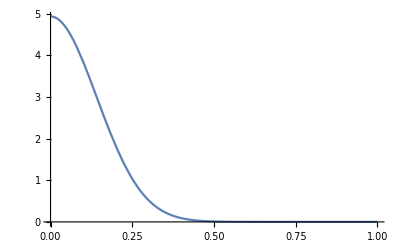

```mathematica
ClearAll["Global`*"];
fv=Exp[-v^2/vth^2];
fz=z;
dlv=1;
dlz=1;
(*mass over z only*)
FullSimplify[Integrate[fv fz dlz,{z,0,Pi}]]
Plot[%/.vth->0.2,{v,0,1}]
```

2D test case with a Jacobian for (r,th) pieces of spherical coordinates

0.098696

0.00394784

0.0194818

1/2 ⅇ^(-v^2/vth^2) π^2 v

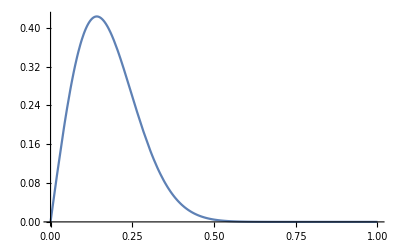

```mathematica
ClearAll["Global`*"];
fv=Exp[-v^2/vth^2];
fz=z;
dlv=v;
dlz=1;
(*mass*)
Integrate[fv fz dlv dlz,{v,0,1},{z,0,Pi}]/.vth->0.2
(*energy*)
Integrate[v^2 fv fz dlv dlz,{v,0,1},{z,0,Pi}]/.vth->0.2
(*some other moment*)
Integrate[v^2 z^2fv fz dlv dlz,{v,0,1},{z,0,Pi}]/.vth->0.2
(*mass over v only*)
(*FullSimplify[Integrate[fv fz jacv,{v,0,1}]]*)
(*mass over z only*)
FullSimplify[Integrate[fv fz dlz,{z,0,Pi}]]
Plot[%/.vth->0.2,{v,0,1}]
```